```mathematica
NSolve[{3x-x^2-2x*y==0,2y-y^2-x*y==0},{x,y}]
```

{{x→3.,y→0.},{x→0.,y→2.},{x→1.,y→1.},{x→0.,y→0.}}

```mathematica
j[x_,y_]=({{3-2x-2y, -2x}, {2-2y-x, -y}})
```

{{3-2 x-2 y,-2 x},{2-x-2 y,-y}}

```mathematica
Eigenvalues[j[3,0]]
```

{1/2 (-3-√33),1/2 (-3+√33)}

```mathematica
Eigenvalues[j[0,2]]
```

{-2,-1}

```mathematica
Eigenvalues[j[1,1]]
```

{-1-√2,-1+√2}

```mathematica
Eigenvalues[j[0,0]]
```

{3,0}

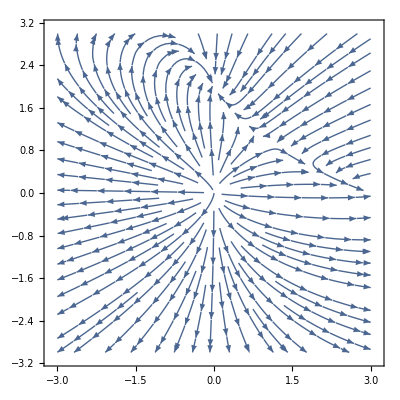

```mathematica
StreamPlot[{3x-x^2-2x*y,2y-y^2-x*y},{x,-3,3},{y,-3,3},Axes->True]
```